```mathematica
n[y_,σ_]:=Gamma[2 y/σ^2](σ^2/2)^(2 y/σ^2);
p[x_,y_,σ_]:=n[y,σ] x^(2 y/σ^2-1)ⅇ^(-2 x/σ^2);
μ[y_,σ_]:=∫_0.1^(+∞) x p[x,y,σ]ⅆx;
var[y_,σ_]:=∫_0.1^(+∞) (x-μ[y,σ])^2 p[x,y,σ]ⅆx;
Print[μ[y,σ]]
Print[var[y,σ]]
```

ConditionalExpression[0.5 4^(-(2 y)/σ^2) (1/σ^2)^(-(2 y)/σ^2) (σ^2)^(1+(2 y)/σ^2) Gamma[(2 y)/σ^2] Gamma[1+(2 y)/σ^2,0.2/σ^2],(Re[y/σ^2]<-1/2&&Re[σ^2]≥0)||Re[σ^2]>0]

ConditionalExpression[0.25 2^(-(12 y)/σ^2) (1/σ^2)^(-(6 y)/σ^2) σ^4 (σ^2)^((2 y)/σ^2) Gamma[(2 y)/σ^2] (2^((8 y)/σ^2) (1/σ^2)^((4 y)/σ^2) Gamma[2+(2 y)/σ^2]+(σ^2)^((2 y)/σ^2) Gamma[(2 y)/σ^2] Gamma[1+(2 y)/σ^2,0.2/σ^2] (-2. 16^(y/σ^2) (1/σ^2)^((2 y)/σ^2) Gamma[1+(2 y)/σ^2]+1. (σ^2)^((2 y)/σ^2) Gamma[(2 y)/σ^2]^2 Gamma[1+(2 y)/σ^2,0.2/σ^2])),Re[y/σ^2]>0&&Re[σ^2]>0]

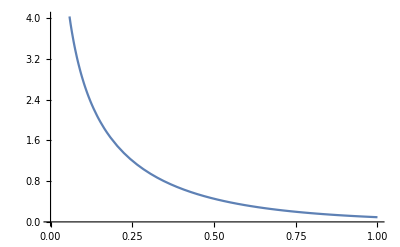

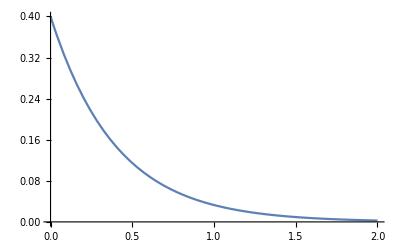

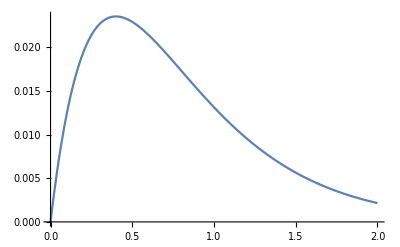

```mathematica
Plot[p[x,0.2,√0.8],{x,0,1}]
Plot[p[x,0.4,√0.8],{x,0,2}]
Plot[p[x,0.8,√0.8],{x,0,2}]
```

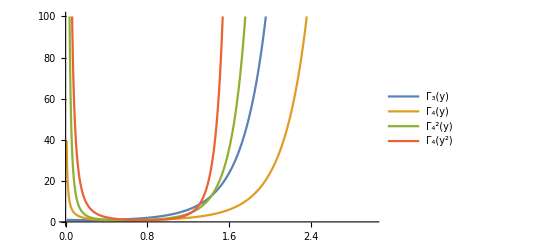

```mathematica
Σ=√0.8;
Subscript[Γ, 3][y_]:=Gamma[1+2 y/Σ^2];
Subscript[Γ, 4][y_]:=Gamma[2 y/Σ^2];
Plot[{Subscript[Γ, 3][y],Subscript[Γ, 4][y], (Subscript[Γ, 4][y])^2, Subscript[Γ, 4][y^2]},{y,0.01,3},PlotRange->{0, 100},PlotLegends->{"Γ_3(y)", "Γ_4(y)", "Γ_4^2(y)", "Γ_4(y^2)"}]
```

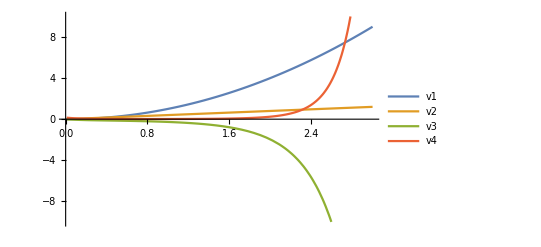

```mathematica
v1[y_]:=y^2;
v2[y_]:=1/2 y Σ^2;
v3[y_]:=-4^(-y/Σ^2)y(1/Σ^2)^(-2 y/Σ^2)Σ^2 Subscript[Γ, 3][y];
v4[y_]:=2^(-4 y/Σ^2)y^2(1/Σ^2)^(-4 y/Σ^2)(Subscript[Γ, 4][y])^2;
Plot[{v1[y],v2[y],v3[y],v4[y]},{y,0.01,3},PlotRange->{-10, 10},PlotLegends->{"v1","v2","v3","v4"}]
```

```mathematica
Limit[y^2 Gamma[y^2], y-> 0]
Limit[y^2(Gamma[y])^2, y-> 0]
Limit[v4[y], y-> 0]
```

1

1

0.16

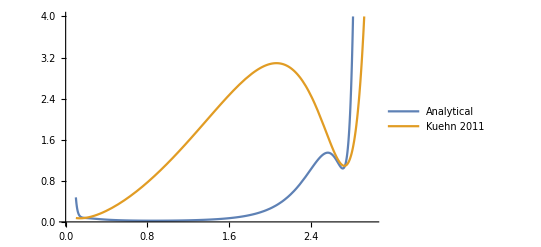

```mathematica
v[y_]:=v1[y]+v2[y]+v3[y]+v4[y];
Plot[{var[y,√0.8],v[y]},{y,0.1,3},PlotRange->{0, 4},PlotLegends->{"Analytical","Kuehn 2011"}]
```